## filtered trajectories from smoldyn

```mathematica
trajectories[filenameserial_?StringQ,filenum_,colour_:Blue]:=Module[{data},
Flatten@Table[
data=Import["C:\\Users\\Ali Hashmi\\Desktop\\research\\brownian simulation of nodal lefty\\nodal lefty\\"<>filenameserial <> ToString[i] <>".txt",{"Data"}]//GroupBy[#,Last]&;
Map[Function[x,data[[x]][[All,{1,2}]]//ListPlot[#,Joined->True,PlotStyle->colour]&],Range[Length@data]],{i,filenum}]
]
```

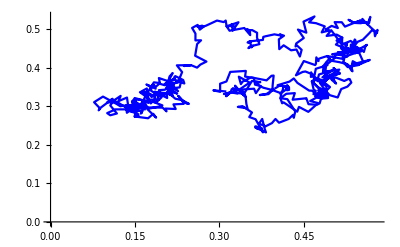
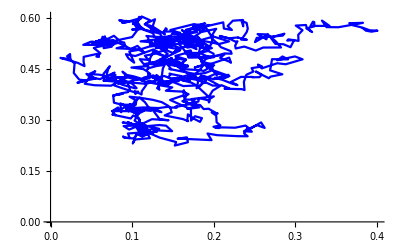
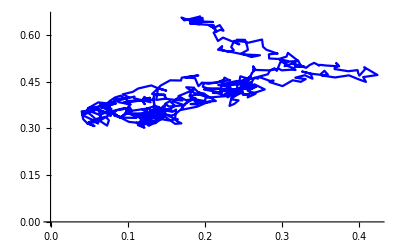
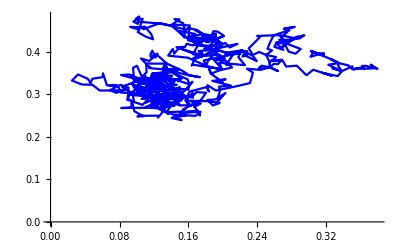
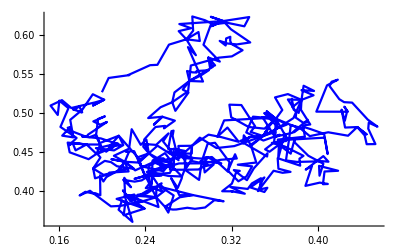
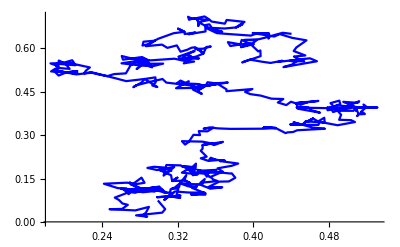
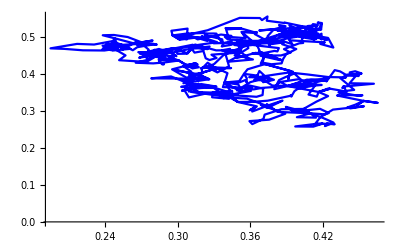
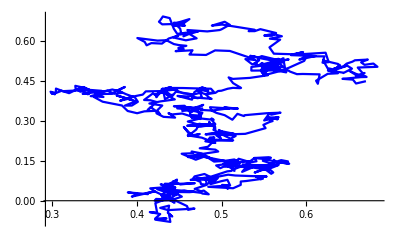

```mathematica
trajectories["nodresmodified",4]
```

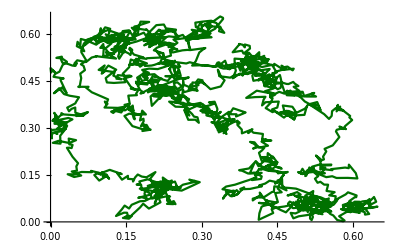
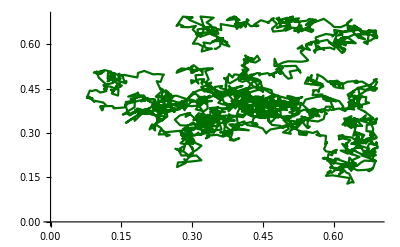
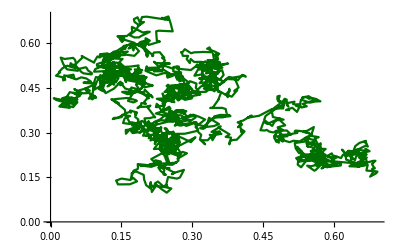
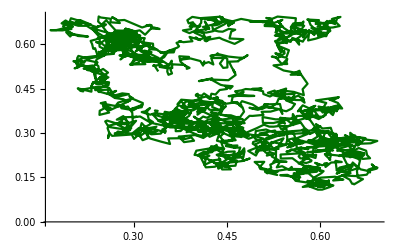
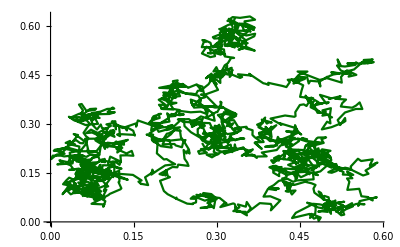
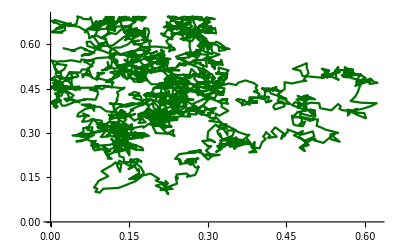
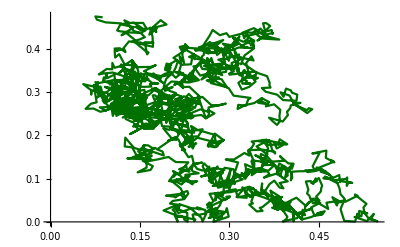
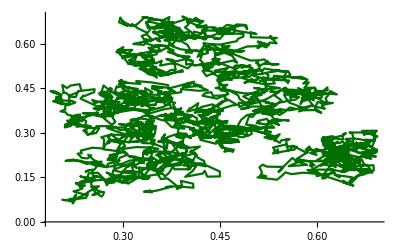

```mathematica
trajectories["leftresmodified",5,Darker@Darker@Green]
```

```mathematica
trajectoriesData[filenameserial_?StringQ,filenum_]:=Module[{data},
Table[
data=Import["C:\\Users\\Ali Hashmi\\Desktop\\research\\brownian simulation of nodal lefty\\nodal lefty\\"<>filenameserial <> ToString[i] <>".txt",{"Data"}]//GroupBy[#,Last]&,{i,filenum}]
]
```

```mathematica
trajdataNodal = trajectoriesData["nodresmodified",4];
```

```mathematica
trajdataLefty = trajectoriesData["leftresmodified",5];
```

```mathematica
trajDataIndexed[trajdata_]:=Association@Flatten[
Module[{data,counter=1},
Table[
data=Thread[Range[counter,counter+(trajdata[[i]]//Length)-1]-> (trajdata[[i]]//Normal)[[All,2,All,{1,2}]]];
counter+=(trajdata[[i]]//Length);data,
{i,Length@trajdata}]
],2]
```

```mathematica
taggedNodal=trajDataIndexed[trajdataNodal];
```

```mathematica
taggedLefty=trajDataIndexed[trajdataLefty];
```

```mathematica
stateDraw[tag_,parnum_,colour_:Blue]:= Module[{data,boundones,boundonesnoInd,boundonesindexed},
data = Table[
Module[{series,totaltimeboundunbound,timesbound,numtimestepbound}, 
series= tag[[i]];
totaltimeboundunbound=(Differences@series)/.{{0.,0.}:> 0,{_,_}:> 1}//Counts;
timesbound=(Differences@series)/.{{0.,0.}:> 0,{_,_}:> 1}//Split//Count[#,Repeated[{0..}]]&;
numtimestepbound = Map[Length,(Differences@series)/.{{0.,0.}:> 0,{_,_}:> 1}//Split//Cases[#,{0..}]&];
{totaltimeboundunbound,timesbound,numtimestepbound}
],{i,parnum}];

boundones = Replace[data,patt:PatternSequence[{_?AssociationQ,_,{}}]:> Sequence[],1];
boundonesnoInd =boundones[[All,3]];
boundonesindexed=MapIndexed[Thread[{#2[[1]],boundonesnoInd[[#]]}]&,Range[Length@boundones]];

GraphicsColumn@{ListPlot[boundonesindexed,PlotStyle-> {colour},PlotLabel -> Style[#,{Bold,FontSize->12,Black}]&@"number of times ligand bound vs how long it remained bound",AxesLabel->{"# of times bound","How long? (# of δt bound)"},ImageSize->Large],GraphicsRow@{Histogram[Flatten@boundones[[All,3]],PlotRange->All,ChartStyle->{XYZColor[0,0,5,0.2]},PlotLabel->Style[#,{Bold,FontSize->12,Black}]&@"counts of stay",ImageSize->Medium],
Histogram[Flatten@boundones[[All,3]],Automatic,"Probability",PlotRange->All,ChartStyle->{XYZColor[0,0,5,0.2]},PlotLabel->Style[#,{Bold,FontSize->12,Black}]&@"probability of stay",ImageSize->Medium]}}
]
```

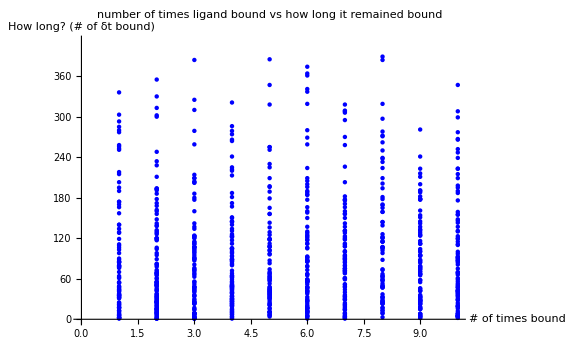

```mathematica
stateDraw[taggedNodal,10]
```

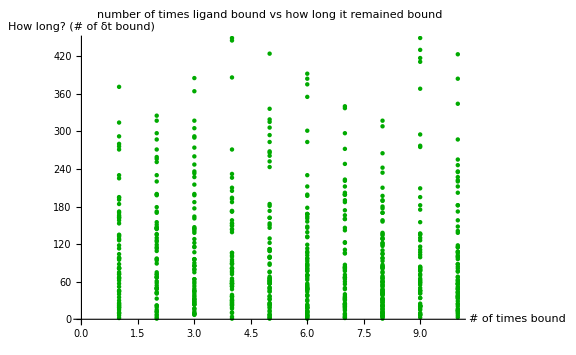

```mathematica
stateDraw[taggedLefty,10,Darker@Green]
```

```mathematica
MSD[tagged_]:=With[{parnum=10,timesteps=1000},
Module[{transposedlist,length},
transposedlist=Transpose@Table[
Thread[{tagged[[j]],RotateLeft[tagged[[j]],i]}][[;;-(i+1)]]
,{j,parnum},{i,timesteps}];

length=(Dimensions/@transposedlist)[[All,2]];

Mean/@Table[
Module[{listreshape,lr},
listreshape=ArrayReshape[transposedlist[[i]],{parnum*length[[i]],2,2}];
lr=Map[Function[x,Power[#,2]&@(Norm@(Subtract@@Reverse@x))],listreshape[[1;;All]]]
],{i,timesteps}]
]
];
```

```mathematica
drNodal = MSD[taggedNodal];
```

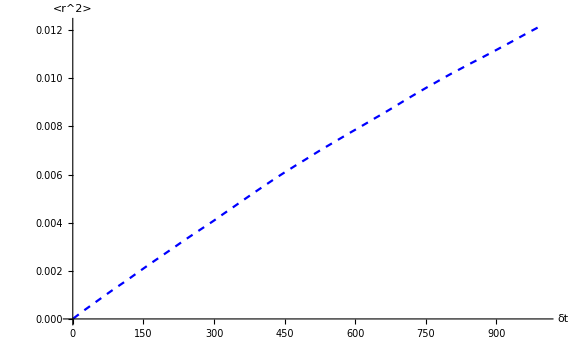

```mathematica
ListPlot[drNodal,AxesLabel-> {"δt", "<r^2>"},PlotStyle->{Dashed,Blue},Joined-> True,ImageSize->Large]
```

```mathematica
p = LinearModelFit[drNodal[[1;;400]],{1,x},x]
```

FittedModel[0.0000500938+0.0000135115 x]

```mathematica
grad = p[[1,2,-1]]
```

0.0000135115

```mathematica
"D_effective simulated with 10 particles for 1000 δt steps: " <> ToString@(grad/(4* 1 10^-6)) <>" um^2/s" <> "\nD_coefficient assumed: " <> ToString@60 <>" um^2/s"
```

D_effective simulated with 10 particles for 1000 δt steps: 3.37787 um^2/s
D_coefficient assumed: 60 um^2/s

```mathematica
drLefty = MSD[taggedLefty];
```

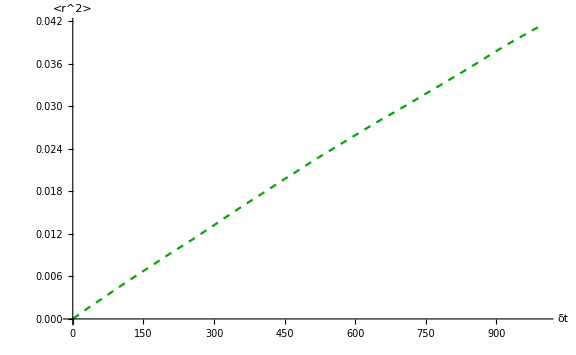

```mathematica
ListPlot[drLefty,AxesLabel-> {"δt", "<r^2>"},PlotStyle->{Dashed,Darker@Green},Joined-> True,ImageSize->Large]
```

```mathematica
p = LinearModelFit[drLefty[[1;;400]],{1,x},x]
```

FittedModel[0.000152536+0.0000436436 x]

```mathematica
grad = p[[1,2,-1]]
```

0.0000436436

```mathematica
"D_effective simulated with 10 particles for 1000 δt steps: " <> ToString@(grad/(4* 1 10^-6)) <>" um^2/s" <> "\nD_coefficient assumed: " <> ToString@60 <>" um^2/s"
```

D_effective simulated with 10 particles for 1000 δt steps: 10.9109 um^2/s
D_coefficient assumed: 60 um^2/s